```mathematica
Pane[Grid[{
{Style["Simulation of HD IDA Surfaces","Chapter"]},
{MouseAppearance[Button[Style["Launch Application","Section"],{ nb=EvaluationNotebook[],NotebookFind[nb,"launchcell",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"]}

}, Alignment->Center,ItemSize->Large,BaselinePosition->Baseline],Alignment->Center,ImageSize->Full]
```

Simulation of HD IDA Surfaces
Launch Application

```mathematica
(* Notebook settings
*)
SetOptions[EvaluationNotebook[],CellContext->Notebook];
SetOptions[$FrontEnd,"DynamicUpdating"->True];
SetOptions[$FrontEnd,"DynamicEvaluationTimeout"->30];

(* Load Packges
*)	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","thermoHD-IDA1.m"}]}]];
Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","thermoHG.m"}]}]];
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","datagen.m"}]}]];
(* Paths
*)
tempPath=FileNameJoin[{NotebookDirectory[],"Parameter","temp-thermoHD-IDA1surface.mx"}];
defaultPath=FileNameJoin[{NotebookDirectory[],"Parameter","default-thermoHD-IDA1surface.mx"}];

initialparameters=Import[defaultPath];
	h0in=initialparameters[[1]];
	d0in=initialparameters[[2]];
	step=initialparameters[[3]];
	kequhdin=initialparameters[[4]];
	sig0in=initialparameters[[5]];
	sigdin=initialparameters[[6]];
	sighdin=initialparameters[[7]];
	ga0in=initialparameters[[8]];
	kequhgain=initialparameters[[9]];

(*Buttons
*)simulationbutton=MouseAppearance[Button["Simulate",{ nb=EvaluationNotebook[],NotebookFind[nb,"simroutineHG",All,CellTags],SelectionEvaluate[nb]},BaseStyle->EdgeForm[Dotted]],"LinkHand"];
variablessavebutton=MouseAppearance[Button["Save Parameters",{
initialparameters={
h0in,
d0in,
step,
kequhdin,
sig0in,
sigdin,
sighdin,
ga0in,
kequhgain
},Export[tempPath,initialparameters]},Appearance->"DialogBox"],"LinkHand"];
variablesloadbutton=MouseAppearance[Button["Load Saved Parameters",{
initialparameters=Import[tempPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhdin=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]],
	ga0in=initialparameters[[8]],
	kequhgain=initialparameters[[9]]
	},Appearance->"DialogBox"],"LinkHand"];

defaultloadbutton=MouseAppearance[Button["Load Default Parameters",{
initialparameters=Import[defaultPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhdin=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]],
	ga0in=initialparameters[[8]],
	kequhgain=initialparameters[[9]]
	},Appearance->"DialogBox"],"LinkHand"];

inputline = {
   {
   Style["species", Bold,Underlined, FontSize->12 ,TextAlignment->Right], 
   Style["concentration", Bold,Underlined, FontSize->12 ,TextAlignment->Right],"",
   Style["binding", Bold,Underlined, FontSize->12 ,TextAlignment->Right]},

   {
   Style["Host:", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[h0in], FieldSize -> 6],"M",
Style["c-step ", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[step], FieldSize -> 6],"M"},
 {"",Dynamic[h0in*1000000],"μM","c-step","","",""},
 
 {Style["Dye:", Bold, FontSize->16 ,TextAlignment->Right], 
   InputField[Dynamic[d0in], FieldSize -> 6],"M",Style["K_equ(HD)" , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[kequhdin], FieldSize -> 6],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[d0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhdin]],""},
 
 
 
   {Style["Guest:", Bold, FontSize->16 ,TextAlignment->Right], 
      InputField[Dynamic[ga0in], FieldSize -> 6],"M",Style["K_equ(HG)" , Bold, FontSize->16 ,TextAlignment->Right],
      InputField[Dynamic[kequhgain], FieldSize -> 6],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[ga0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhgain]],""},
   
   
   {Style["Signal-HD", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[sighdin], FieldSize -> 6],"",
   
   Style["Signal-D", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sigdin], FieldSize -> 6],"",
   Style["Signal-0", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sig0in], FieldSize -> 6]},
      {"HD complex","","","dye alone","","","Startsignal"}  
    
};

Print[TableForm[{{simulationbutton,variablesloadbutton,variablessavebutton,defaultloadbutton}}]];

Print[TableForm[inputline, TableAlignments -> Left]];
Print[Style["IDA - ",Bold],Style["Indicator Displacement Assay ",Italic,Bold,FontColor->Gray],Style["ADA - ",Bold],Style["Analyte Displacement Assay ",Italic,Bold,FontColor->Gray],Style["SAIBA - ",Bold],Style["Simultaneous Analyte and Indicator Binding Assay ",Italic,Bold,FontColor->Gray]];
```

Simulate | Load Saved Parameters | Save Parameters | Load Default Parameters

species | concentration |  | binding |  |  |  | 
Host: |  | M | c-step  |  | M |  | 
 |  | μM | c-step |  |  |  | 
Dye: |  | M | K_equ(HD) |  | M^-1 |  | 
 |  | μM | lg(K_equ) |  |  |  | 
Guest: |  | M | K_equ(HG) |  | M^-1 |  | 
 |  | μM | lg(K_equ) |  |  |  | 
Signal-HD |  |  | Signal-D |  |  | Signal-0 | 
HD complex |  |  | dye alone |  |  | Startsignal |

IDA - Indicator Displacement Assay ADA - Analyte Displacement Assay SAIBA - Simultaneous Analyte and Indicator Binding Assay

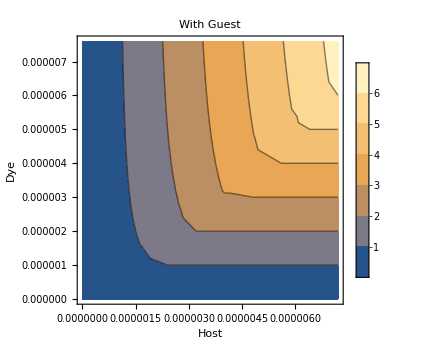
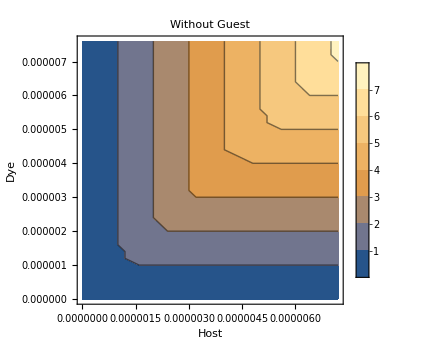
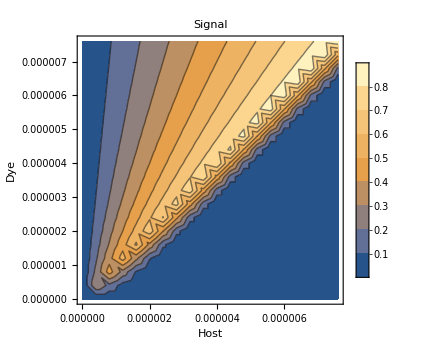
-Graphics- | -Graphics-
-Graphics- | You can save simulated data:
Save-Sim

```mathematica
mode="Ga0 varied";
start=1.0×10^-15;

dataHD1=Table[{N[i],N[j],1000000*sthdidaHD[kequhdin,kequhgain,i,j,ga0in]},{i,start,h0in,h0in/10},{j,start,d0in,d0in/20}];
dataHD2=Table[{N[i],N[j],1000000*sthgSignal[kequhdin,i,j,sig0in,sighdin,sigdin]},{i,start,h0in,h0in/10},{j,start,d0in,d0in/20}];
dataHD3=Table[{N[i],N[j],1000000*Abs[sthdidaHD[kequhdin,kequhgain,i,j,ga0in]-sthgSignal[kequhdin,i,j,sig0in,sighdin,sigdin]]},{i,start,h0in,h0in/20},{j,start,d0in,d0in/20}];



inputs={{"Quantity","Value"},
{"Mode",mode},
{"conc(H)",h0in},
{"conc(D)",d0in},
{"Kequ(HD2)",kequhdin},
{"conc(G)",ga0in},
{"Kequ(HG)",kequhgain},
{"Signal-0",sig0in},
{"Signal-HD",sighdin},
{"Signal-Dye",sigdin},
{"c-step",step}
};
header={"conc-Host","conc-Dye","Signal","HD-Guest","HD-0"};
units={"M","M","M","M"};
column1=Flatten[inputs[[All,1]]];
column2=Flatten[inputs[[All,2]]];

signaloutput=Join[Flatten[dataHD3,1],List/@Flatten[dataHD1,1][[All,3]],List/@Flatten[dataHD2,1][[All,3]],2];



put=Prepend[Prepend[signaloutput,units],header];
output=Join[put,List/@column1,List/@column2,2];


Quiet[exportbutton2=Button["Save-Sim",Export[SystemDialogInput["FileSave",".csv"],output],Method->"Queued"]];

simplot3=Grid[{{ListContourPlot[Flatten[dataHD1,1],ImageSize->Medium,PlotLabel-> "With Guest",PlotLegends->Automatic,FrameLabel->{"Host","Dye"}],ListContourPlot[Flatten[dataHD2,1],ImageSize->Medium,PlotLabel-> "Without Guest",PlotLegends->Automatic,FrameLabel->{"Host","Dye"}]},{ListContourPlot[Flatten[dataHD3,1],ImageSize->Medium,PlotLabel-> "Signal",PlotLegends->Automatic,FrameLabel->{"Host","Dye"}]}}];

Print[simplot3,TableForm[{"You can save simulated data:",exportbutton2}]];

Off[Export::chtype];
```

```mathematica
f=Interpolation[Flatten[dataHD3,1]]
Plot3D[f[x,y],{x,0,h0in},{y,0,d0in}]
```

-15        -6         -15        -6
InterpolatingFunction[{{1. 10   , 7.6 10  }, {1. 10   , 7.6 10  }}, <>]

-Graphics3D-

```mathematica
Sum
```

InterpolatingFunction::dmvali: The integration endpoint 8.×10^-6 in dimension 2 lies outside the range of data in the interpolating function. Extrapolation will be used.

1.53513×10^-11